```mathematica
Rsun=6.9598*10^10;
```

```mathematica
GONGdata0=Drop[Drop[Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\GONGdata","Table"],1],-1];
```

```mathematica
GONGdata1=GONGdata0;
For[i=1,i≤Dimensions[GONGdata1][[1]],i=i+1,GONGdata1[[i]][[2]]=1.5708-GONGdata0[[i]][[2]]]
GONGdata=GONGdata1;
For[i=1,i≤Dimensions[GONGdata1][[1]],i=i+1,GONGdata[[i]][[3]]=GONGdata1[[i]][[3]]*10^-9*2*Pi]
```

```mathematica
RadiusThetaOmegaSq=Table[{GONGdata[[i]][[1]],GONGdata[[i]][[2]],{GONGdata[[i]][[3]]^2}},{i,1,Dimensions[GONGdata][[1]]}];
```

```mathematica
OmegaSqN=Interpolation[RadiusThetaOmegaSq];
```

```mathematica
TemporaryTable=Table[{r,Table[{theta,OmegaSqN[r,theta][[1]]},{theta,0,1.57,0.01}]},{r,0.5,1,0.01}];
RadiusOmegaSqNTable=Table[{TemporaryTable[[i]][[1]],LinearModelFit[TemporaryTable[[i]][[2]],{1,Cos[theta]^2},theta]["BestFitParameters"]},{i,1,Dimensions[TemporaryTable][[1]]}];
```

```mathematica
OmegaSq0Table=Table[{RadiusOmegaSqNTable[[i]][[1]],RadiusOmegaSqNTable[[i]][[2]][[1]]},{i,1,Dimensions[RadiusOmegaSqNTable][[1]]}];
OmegaSq2Table=Table[{RadiusOmegaSqNTable[[i]][[1]],RadiusOmegaSqNTable[[i]][[2]][[2]]},{i,1,Dimensions[RadiusOmegaSqNTable][[1]]}];
```

```mathematica
rMin=0.58;
rMax=0.76;
```

```mathematica
OmegaSq0TableReduced=Select[OmegaSq0Table,rMin<#[[1]]<rMax&];
OmegaSq2TableReduced=Select[OmegaSq2Table,rMin<#[[1]]<rMax&];
```

```mathematica
Polinomi=Table[q^i,{i,0,4}];
```

```mathematica
OmegaSq0=Fit[OmegaSq0TableReduced,Polinomi,q];
OmegaSq0Fit[x_]=OmegaSq0/.{q->x};

OmegaSq2=Fit[OmegaSq2TableReduced,Polinomi,q];
OmegaSq2Fit[x_]=OmegaSq2/.{q->x};
```

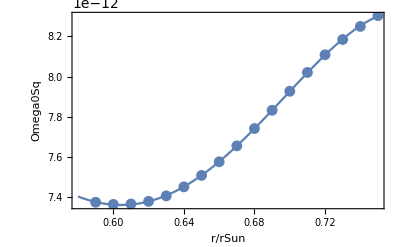

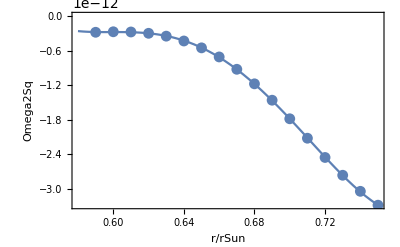

```mathematica
Show[Plot[OmegaSq0Fit[r],{r,rMin,0.75}],ListPlot[OmegaSq0TableReduced],Frame->True,FrameLabel->{"r/rSun",Omega0Sq}]
Show[Plot[OmegaSq2Fit[r],{r,rMin,0.75}],ListPlot[OmegaSq2TableReduced],Frame->True,FrameLabel->{"r/rSun",Omega2Sq}]
```

```mathematica
rStart=0.60;
OmegaSq0Fit[rStart];
OmegaSq0Fit'[rStart]/Rsun;
OmegaSq0Fit''[rStart]/Rsun^2;
OmegaSq2Fit[rStart];
OmegaSq2Fit'[rStart]/Rsun;
OmegaSq2Fit''[rStart]/Rsun^2;
```